```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/linear-stability

```mathematica
dim=100
dspeed=1
odspeed=1
scale=1
```

100

1

1

1

```mathematica
mat[n_,scale_,kd_,koff_]:=Module[{matM,diagM,midM},

matM=IdentityMatrix[n];
midM=Floor[n/2];
(*
diagM=ReplacePart[
matM,
{i_,i_}:>RandomReal[1]
];*)


Do[
matM[[midM+i,midM+i]]= scale i+kd RandomReal[1],
{i,-midM+1,midM-1}
];


(*Do[
matM[[midM+i,midM+i+1]]=k i,
{i,-midM+1,midM-1}
];

Do[
matM[[midM+i+1,midM+i]]=k i,
{i,-midM+1,midM-1}
];*)

Do[
matM[[midM+i,midM+i+1]]=koff RandomReal[1],
{i,-midM+1,midM-1}
];

Do[
matM[[midM+i+1,midM+i]]=koff RandomReal[1],
{i,-midM+1,midM-1}
];

matM[[1,dim]]=koff RandomReal[1];
matM[[dim,1]]=koff RandomReal[1];

matM

]
```

```mathematica
mat[dim,0.1,1,1]//MatrixForm
```

(0.101717 | 0.610631 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.600326
0.778951 | 0.511977 | 0.287933 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.615279 | 0.43542 | 0.504122 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.267337 | 0.257154 | 0.213887 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.50618 | 0.828659 | 0.622606 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.623192 | 0.423603 | 0.267592 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.791907 | 0.786113 | 0.785945 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.22902 | 0.659276 | 0.298973 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.902883 | 0.613851 | 0.700735
0.450311 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.420158 | 1)

```mathematica
Eigensystem@mat[dim,1,1,1]//MatrixForm
```

(5.01752 | -3.82778 | 3.24091 | 2.88755 | -2.40589 | 2.00246 | -1.6188 | 0.817236 | 0.619746 | 0.0649898
{-5.76032×10^-8,-6.55721×10^-7,-0.0000203051,-0.000149091,-0.00405021,-0.0183962,-0.12309,-0.42983,-0.871667,-0.199841} | {0.825117,-0.545097,0.143176,-0.0388714,0.00639942,-0.000641433,0.0000367331,-2.84903×10^-7,6.94107×10^-9,-1.32425×10^-9} | {-6.62079×10^-6,-0.000059351,-0.00141009,-0.00737888,-0.127666,-0.338917,-0.914851,-0.177082,0.0200375,0.00823592} | {0.000013148,0.000111537,0.00248956,0.0119817,0.183427,0.417621,0.780057,-0.42591,0.0392737,0.0191644} | {0.513834,0.655381,-0.502483,0.225473,-0.0553849,0.00746651,-0.00054053,5.28981×10^-6,-1.56399×10^-7,4.22957×10^-8} | {-0.000109476,-0.00079677,-0.0149068,-0.0560341,-0.573237,-0.756506,0.308979,-0.0162585,0.000970334,0.00089155} | {0.0980979,0.230255,0.775321,-0.548285,0.186145,-0.0310351,0.00263169,-0.0000301265,1.01484×10^-6,-3.56933×10^-7} | {0.0000393683,0.000222989,0.00308561,0.00722793,0.0215978,-0.00237337,-0.0209842,0.0822629,-0.193877,0.977072} | {-0.00309131,-0.0166784,-0.217146,-0.457179,-0.762675,0.396924,-0.0657461,0.00148134,-0.000133488,0.00032334} | {-0.00481697,-0.0223503,-0.239312,-0.343797,0.858643,-0.291913,0.0390984,-0.000705014,0.0000368498,-0.0000363003})

```mathematica
eigensys=Transpose@Sort[Transpose@Eigensystem[mat[dim,1,1,1]],#1[[1]]<#2[[1]]&];
```

```mathematica
eigensys[[1]]
```

{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485}

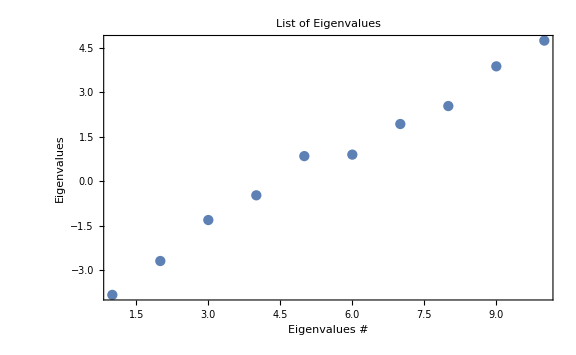

```mathematica
ListPlot[
eigensys[[1]],
Frame->True,ImageSize->Large,PlotRange->Full,FrameLabel->{"Eigenvalues #","Eigenvalues"},PlotLabel->"List of Eigenvalues"
]
```

```mathematica
Transpose[solList][[100;;100]]
Transpose[solList][[100]]
```

{{{9.9,3.55102×10^-6},{9.9,0.0000237891},{9.9,0.0000233004},{9.9,0.000593887},{9.9,0.000656826},{9.9,0.00111383},{9.9,0.0000577068},{9.9,0.0000233269},{9.9,2.29544×10^-6},{9.9,4.06678×10^-6}}}

{{9.9,3.55102×10^-6},{9.9,0.0000237891},{9.9,0.0000233004},{9.9,0.000593887},{9.9,0.000656826},{9.9,0.00111383},{9.9,0.0000577068},{9.9,0.0000233269},{9.9,2.29544×10^-6},{9.9,4.06678×10^-6}}

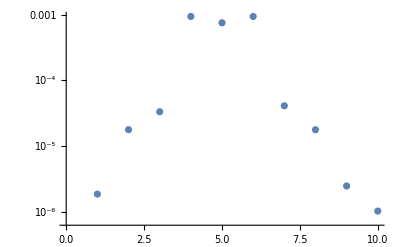

```mathematica
ListLogPlot[
#[[2]]&/@Transpose[solList][[20]]
]
```

```mathematica
Dimensions@(
Transpose[solList][[Length@Transpose[solList];;]]
)
```

{1,10,2}

```mathematica
Transpose[solList][[Length@solList;;]]
```

{{{0.9,1.48997×10^-7},{0.9,2.91402×10^-6},{0.9,0.0000116714},{0.9,0.000588485},{0.9,0.000932918},{0.9,0.000516364},{0.9,0.0000117011},{0.9,2.92424×10^-6},{0.9,2.10184×10^-7},{0.9,3.76524×10^-8}},190,{{20.,4.55431×10^-6},{20.,0.0000276411},{20.,0.0000343108},{20.,0.000913332},{20.,0.000885353},{20.,0.000623565},{20.,0.0000534068},{20.,0.000024075},{20.,2.68962×10^-6},{20.,7.52593×10^-6}}}
 |  |  |  |

Part::take: Cannot take positions 19 through 22 in {{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},«7»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}.

ListLogPlot::lpn: {{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},«8»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,19;;22⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Part::take: Cannot take positions 30 through 32 in {{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},«7»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}.

Part::take: Cannot take positions 38 through 40 in {{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},«7»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}.

General::stop: Further output of Part::take will be suppressed during this calculation.

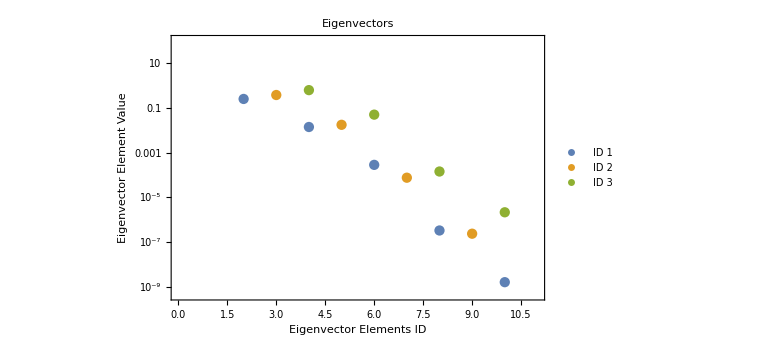
-Graphics- | ListLogPlot[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},{-0.0907672,-0.219176,-0.732192,0.61375,-0.168799,0.0493391,-0.00142902,0.000142566,-7.17896×10^-6,2.15331×10^-6},{0.0133516,0.0440258,0.243651,0.868034,-0.400011,0.158087,-0.00585998,0.000695936,-0.0000419933,0.0000197059},{0.000374018,0.0017565,0.0157305,0.159101,0.732777,-0.659848,0.0441537,-0.0077116,0.00178022,-0.00792282},{1.78343×10^-6,8.46982×10^-6,0.0000769422,0.000796975,0.00381557,-0.00149855,-0.00464975,0.026393,-0.150839,0.988186},{-0.0000112283,-0.0000655907,-0.000769773,-0.0118322,-0.100678,-0.974015,0.195739,-0.0516241,0.00499666,0.00373996},{2.29667×10^-6,0.0000148892,0.000197862,0.00362047,0.0386537,0.596278,0.747376,-0.287502,0.0377489,0.0170804},{-3.41304×10^-8,-2.69632×10^-7,-4.50656×10^-6,-0.000111497,-0.00172229,-0.0482352,-0.209696,-0.900727,0.366801,0.0885738},{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,19;;22⟧,Frame→True,ImageSize→Large,PlotLegends→Placed[{ID 19,ID 20,ID 21,ID 22},{Left,Top}],PlotRange→{{0,11},{Automatic,100}},Filling→Axis,FrameLabel→{Eigenvector Elements ID,Eigenvector Element Value},PlotLabel→Eigenvectors]
ListLogPlot[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},{-0.0907672,-0.219176,-0.732192,0.61375,-0.168799,0.0493391,-0.00142902,0.000142566,-7.17896×10^-6,2.15331×10^-6},{0.0133516,0.0440258,0.243651,0.868034,-0.400011,0.158087,-0.00585998,0.000695936,-0.0000419933,0.0000197059},{0.000374018,0.0017565,0.0157305,0.159101,0.732777,-0.659848,0.0441537,-0.0077116,0.00178022,-0.00792282},{1.78343×10^-6,8.46982×10^-6,0.0000769422,0.000796975,0.00381557,-0.00149855,-0.00464975,0.026393,-0.150839,0.988186},{-0.0000112283,-0.0000655907,-0.000769773,-0.0118322,-0.100678,-0.974015,0.195739,-0.0516241,0.00499666,0.00373996},{2.29667×10^-6,0.0000148892,0.000197862,0.00362047,0.0386537,0.596278,0.747376,-0.287502,0.0377489,0.0170804},{-3.41304×10^-8,-2.69632×10^-7,-4.50656×10^-6,-0.000111497,-0.00172229,-0.0482352,-0.209696,-0.900727,0.366801,0.0885738},{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,30;;32⟧,Frame→True,ImageSize→Large,PlotLegends→Placed[{ID 30,ID 31,ID 32},{Left,Top}],PlotRange→{{0,11},{Automatic,100}},Filling→Axis,FrameLabel→{Eigenvector Elements ID,Eigenvector Element Value},PlotLabel→Eigenvectors] | ListLogPlot[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},{-0.0907672,-0.219176,-0.732192,0.61375,-0.168799,0.0493391,-0.00142902,0.000142566,-7.17896×10^-6,2.15331×10^-6},{0.0133516,0.0440258,0.243651,0.868034,-0.400011,0.158087,-0.00585998,0.000695936,-0.0000419933,0.0000197059},{0.000374018,0.0017565,0.0157305,0.159101,0.732777,-0.659848,0.0441537,-0.0077116,0.00178022,-0.00792282},{1.78343×10^-6,8.46982×10^-6,0.0000769422,0.000796975,0.00381557,-0.00149855,-0.00464975,0.026393,-0.150839,0.988186},{-0.0000112283,-0.0000655907,-0.000769773,-0.0118322,-0.100678,-0.974015,0.195739,-0.0516241,0.00499666,0.00373996},{2.29667×10^-6,0.0000148892,0.000197862,0.00362047,0.0386537,0.596278,0.747376,-0.287502,0.0377489,0.0170804},{-3.41304×10^-8,-2.69632×10^-7,-4.50656×10^-6,-0.000111497,-0.00172229,-0.0482352,-0.209696,-0.900727,0.366801,0.0885738},{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,38;;40⟧,Frame→True,ImageSize→Large,PlotLegends→Placed[{ID 38,ID 39,ID 40},{Left,Top}],PlotRange→{{0,11},{Automatic,100}},Filling→Axis,FrameLabel→{Eigenvector Elements ID,Eigenvector Element Value},PlotLabel→Eigenvectors]

```mathematica
{{
ListLogPlot[
eigensys[[2,1;;3]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,1,3}]),{Right,Top}],PlotRange->{{0,dim+1},{Automatic,100}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Eigenvector Element Value"},PlotLabel->"Eigenvectors"
],

ListLogPlot[
eigensys[[2,19;;22]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,19,22}]),{Left,Top}],PlotRange->{{0,dim+1},{Automatic,100}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Eigenvector Element Value"},PlotLabel->"Eigenvectors"
]
},
{
ListLogPlot[
eigensys[[2,30;;32]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,30,32}]),{Left,Top}],PlotRange->{{0,dim+1},{Automatic,100}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Eigenvector Element Value"},PlotLabel->"Eigenvectors"
],

ListLogPlot[
eigensys[[2,38;;40]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,38,40}]),{Left,Top}],PlotRange->{{0,dim+1},{Automatic,100}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Eigenvector Element Value"},PlotLabel->"Eigenvectors"
]
}}//Grid

(*Export["eigenvectors-logplot-of-pseudo-hamiltonian-scale-4.png",%]*)
```

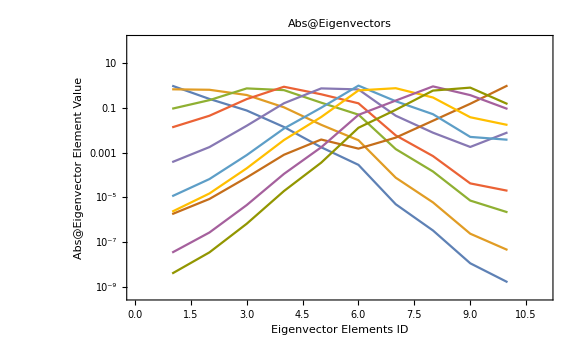

```mathematica
ListLogPlot[
Abs@eigensys[[2,;;]],
Frame->True,Joined->True,ImageSize->Large,PlotRange->{{0,dim+1},{Automatic,100}},FrameLabel->{"Eigenvector Elements ID","Abs@Eigenvector Element Value"},PlotLabel->"Abs@Eigenvectors"
]
```

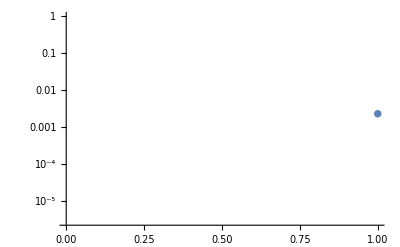

-13.9667-4.61776 x

```mathematica
ListLogPlot@Abs@(Transpose@Sort[Transpose@Eigensystem[mat[dim,0.1,1,1]],#1[[1]]<#2[[1]]&])[[2,1]][[10;;]]

Fit[Log@Abs@(Transpose@Sort[Transpose@Eigensystem[mat[dim,10,1,1]],#1[[1]]<#2[[1]]&])[[2,1]][[5;;]],{1,x},x]
```

```mathematica
ArrayReshape[{a,b,c,d,e,f},{3,2}]
```

{{a,b},{c,d},{e,f}}

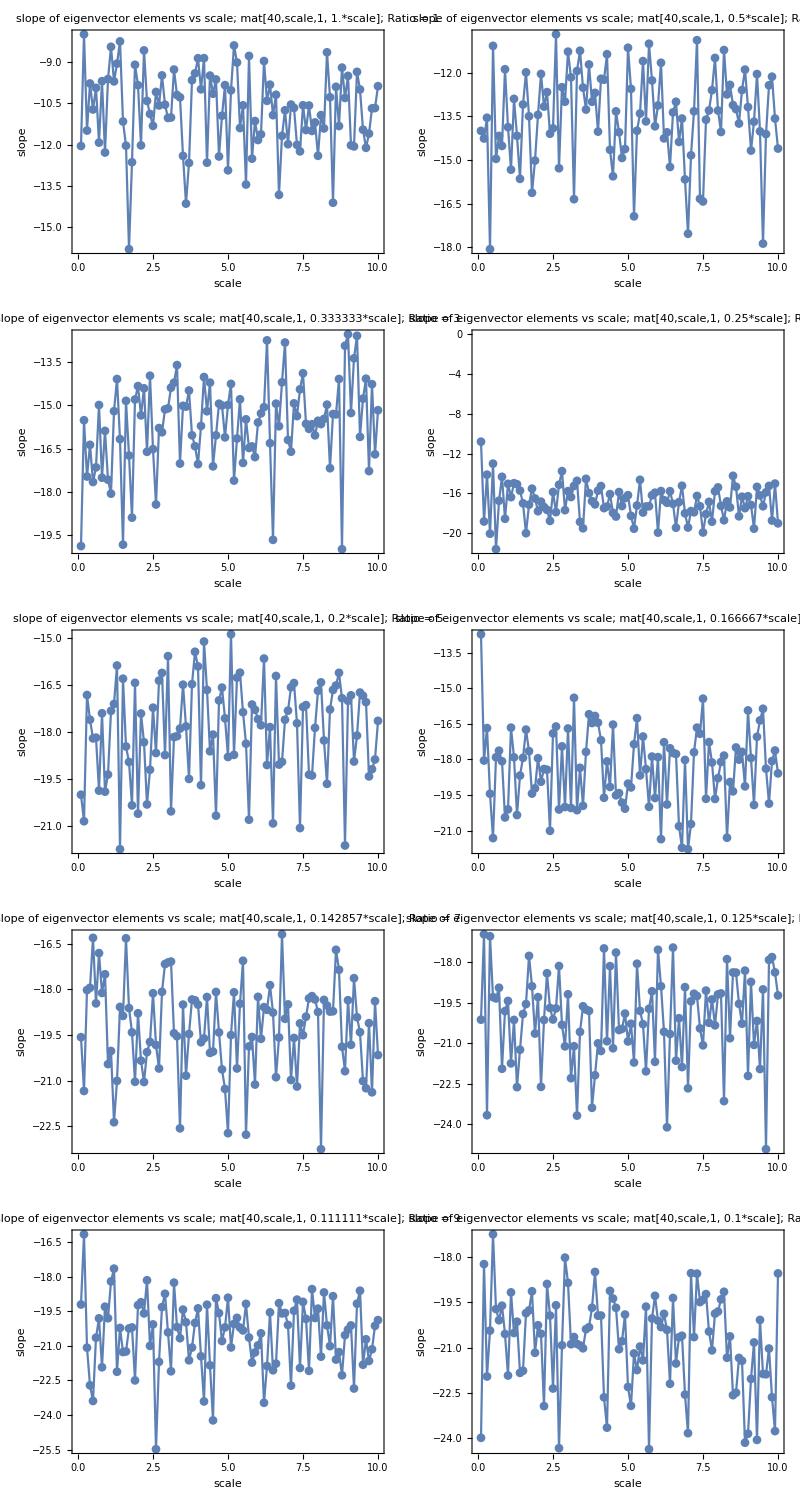

```mathematica
ArrayReshape[
Table[

ListPlot[
Table[
{scaleN,Coefficient[
Fit[Log@Abs@(Transpose@Sort[Transpose@Eigensystem[mat[dim,scaleN,1,scaleN/ratio]],#1[[1]]<#2[[1]]&])[[2,1]][[10;;]],{1,x},x],
x
]
},
{scaleN,0.1,10,0.1}
],
Frame->True,PlotLabel->"slope of eigenvector elements vs scale; mat[40,scale,1, "<>ToString[N@1/ratio]<>"*scale]"<>"; Ratio = "<>ToString@ratio,ImageSize->Large,FrameLabel->{"scale","slope"},Joined->True,PlotMarkers->Automatic
],
{ratio,1,10,1}
],
{5,2}
]//Grid
```

```mathematica
(*Export["slope-log-eigenvector-elements-vs-scale-ratio-1-to-10.png",%]*)
```

Part::take: Cannot take positions 19 through 22 in {{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},«7»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}.

ListLogPlot::lpn: Abs[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},«8»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,19;;22⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Part::take: Cannot take positions 30 through 32 in {{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},«7»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}.

Part::take: Cannot take positions 38 through 40 in {{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},«7»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}.

General::stop: Further output of Part::take will be suppressed during this calculation.

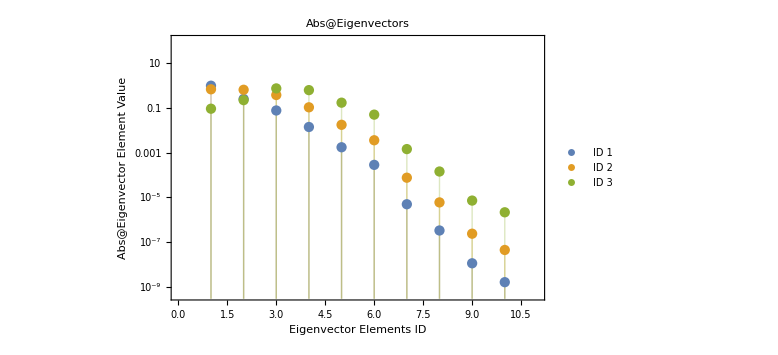
-Graphics- | ListLogPlot[Abs[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},{-0.0907672,-0.219176,-0.732192,0.61375,-0.168799,0.0493391,-0.00142902,0.000142566,-7.17896×10^-6,2.15331×10^-6},{0.0133516,0.0440258,0.243651,0.868034,-0.400011,0.158087,-0.00585998,0.000695936,-0.0000419933,0.0000197059},{0.000374018,0.0017565,0.0157305,0.159101,0.732777,-0.659848,0.0441537,-0.0077116,0.00178022,-0.00792282},{1.78343×10^-6,8.46982×10^-6,0.0000769422,0.000796975,0.00381557,-0.00149855,-0.00464975,0.026393,-0.150839,0.988186},{-0.0000112283,-0.0000655907,-0.000769773,-0.0118322,-0.100678,-0.974015,0.195739,-0.0516241,0.00499666,0.00373996},{2.29667×10^-6,0.0000148892,0.000197862,0.00362047,0.0386537,0.596278,0.747376,-0.287502,0.0377489,0.0170804},{-3.41304×10^-8,-2.69632×10^-7,-4.50656×10^-6,-0.000111497,-0.00172229,-0.0482352,-0.209696,-0.900727,0.366801,0.0885738},{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,19;;22⟧],Frame→True,ImageSize→Large,PlotLegends→Placed[{ID 19,ID 20,ID 21,ID 22},{Left,Top}],PlotRange→{{0,11},{Automatic,100}},Filling→Axis,FrameLabel→{Eigenvector Elements ID,Abs@Eigenvector Element Value},PlotLabel→Abs@Eigenvectors]
ListLogPlot[Abs[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},{-0.0907672,-0.219176,-0.732192,0.61375,-0.168799,0.0493391,-0.00142902,0.000142566,-7.17896×10^-6,2.15331×10^-6},{0.0133516,0.0440258,0.243651,0.868034,-0.400011,0.158087,-0.00585998,0.000695936,-0.0000419933,0.0000197059},{0.000374018,0.0017565,0.0157305,0.159101,0.732777,-0.659848,0.0441537,-0.0077116,0.00178022,-0.00792282},{1.78343×10^-6,8.46982×10^-6,0.0000769422,0.000796975,0.00381557,-0.00149855,-0.00464975,0.026393,-0.150839,0.988186},{-0.0000112283,-0.0000655907,-0.000769773,-0.0118322,-0.100678,-0.974015,0.195739,-0.0516241,0.00499666,0.00373996},{2.29667×10^-6,0.0000148892,0.000197862,0.00362047,0.0386537,0.596278,0.747376,-0.287502,0.0377489,0.0170804},{-3.41304×10^-8,-2.69632×10^-7,-4.50656×10^-6,-0.000111497,-0.00172229,-0.0482352,-0.209696,-0.900727,0.366801,0.0885738},{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,30;;32⟧],Frame→True,ImageSize→Large,PlotLegends→Placed[{ID 30,ID 31,ID 32},{Left,Top}],PlotRange→{{0,11},{Automatic,100}},Filling→Axis,FrameLabel→{Eigenvector Elements ID,Abs@Eigenvector Element Value},PlotLabel→Abs@Eigenvectors] | ListLogPlot[Abs[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},{-0.0907672,-0.219176,-0.732192,0.61375,-0.168799,0.0493391,-0.00142902,0.000142566,-7.17896×10^-6,2.15331×10^-6},{0.0133516,0.0440258,0.243651,0.868034,-0.400011,0.158087,-0.00585998,0.000695936,-0.0000419933,0.0000197059},{0.000374018,0.0017565,0.0157305,0.159101,0.732777,-0.659848,0.0441537,-0.0077116,0.00178022,-0.00792282},{1.78343×10^-6,8.46982×10^-6,0.0000769422,0.000796975,0.00381557,-0.00149855,-0.00464975,0.026393,-0.150839,0.988186},{-0.0000112283,-0.0000655907,-0.000769773,-0.0118322,-0.100678,-0.974015,0.195739,-0.0516241,0.00499666,0.00373996},{2.29667×10^-6,0.0000148892,0.000197862,0.00362047,0.0386537,0.596278,0.747376,-0.287502,0.0377489,0.0170804},{-3.41304×10^-8,-2.69632×10^-7,-4.50656×10^-6,-0.000111497,-0.00172229,-0.0482352,-0.209696,-0.900727,0.366801,0.0885738},{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,38;;40⟧],Frame→True,ImageSize→Large,PlotLegends→Placed[{ID 38,ID 39,ID 40},{Left,Top}],PlotRange→{{0,11},{Automatic,100}},Filling→Axis,FrameLabel→{Eigenvector Elements ID,Abs@Eigenvector Element Value},PlotLabel→Abs@Eigenvectors]

```mathematica
{{
ListLogPlot[
Abs@eigensys[[2,1;;3]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,1,3}]),{Right,Top}],PlotRange->{{0,dim+1},{Automatic,100}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Abs@Eigenvector Element Value"},PlotLabel->"Abs@Eigenvectors"
],

ListLogPlot[
Abs@eigensys[[2,19;;22]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,19,22}]),{Left,Top}],PlotRange->{{0,dim+1},{Automatic,100}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Abs@Eigenvector Element Value"},PlotLabel->"Abs@Eigenvectors"
]
},
{
ListLogPlot[
Abs@eigensys[[2,30;;32]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,30,32}]),{Left,Top}],PlotRange->{{0,dim+1},{Automatic,100}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Abs@Eigenvector Element Value"},PlotLabel->"Abs@Eigenvectors"
],

ListLogPlot[
Abs@eigensys[[2,38;;40]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,38,40}]),{Left,Top}],PlotRange->{{0,dim+1},{Automatic,100}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Abs@Eigenvector Element Value"},PlotLabel->"Abs@Eigenvectors"
]
}}//Grid

(*Export["eigenvectors-absolute-values-logplot-of-pseudo-hamiltonian-scale-1.png",%]*)
```

Part::take: Cannot take positions 20 through 22 in {{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},«7»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}.

ListPlot::lpn: {{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},«8»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,20;;22⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::take: Cannot take positions 30 through 32 in {{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},«7»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}.

Part::take: Cannot take positions 38 through 40 in {{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},«7»,{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}.

General::stop: Further output of Part::take will be suppressed during this calculation.

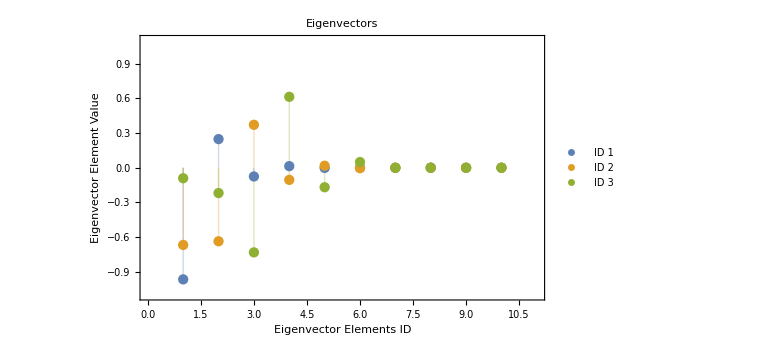
-Graphics- | ListPlot[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},{-0.0907672,-0.219176,-0.732192,0.61375,-0.168799,0.0493391,-0.00142902,0.000142566,-7.17896×10^-6,2.15331×10^-6},{0.0133516,0.0440258,0.243651,0.868034,-0.400011,0.158087,-0.00585998,0.000695936,-0.0000419933,0.0000197059},{0.000374018,0.0017565,0.0157305,0.159101,0.732777,-0.659848,0.0441537,-0.0077116,0.00178022,-0.00792282},{1.78343×10^-6,8.46982×10^-6,0.0000769422,0.000796975,0.00381557,-0.00149855,-0.00464975,0.026393,-0.150839,0.988186},{-0.0000112283,-0.0000655907,-0.000769773,-0.0118322,-0.100678,-0.974015,0.195739,-0.0516241,0.00499666,0.00373996},{2.29667×10^-6,0.0000148892,0.000197862,0.00362047,0.0386537,0.596278,0.747376,-0.287502,0.0377489,0.0170804},{-3.41304×10^-8,-2.69632×10^-7,-4.50656×10^-6,-0.000111497,-0.00172229,-0.0482352,-0.209696,-0.900727,0.366801,0.0885738},{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,20;;22⟧,Frame→True,ImageSize→Large,PlotLegends→Placed[{ID 20,ID 21,ID 22},{Left,Top}],PlotRange→{{0,11},{-1.1,1.1}},Filling→Axis,FrameLabel→{Eigenvector Elements ID,Eigenvector Element Value},PlotLabel→Eigenvectors]
ListPlot[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},{-0.0907672,-0.219176,-0.732192,0.61375,-0.168799,0.0493391,-0.00142902,0.000142566,-7.17896×10^-6,2.15331×10^-6},{0.0133516,0.0440258,0.243651,0.868034,-0.400011,0.158087,-0.00585998,0.000695936,-0.0000419933,0.0000197059},{0.000374018,0.0017565,0.0157305,0.159101,0.732777,-0.659848,0.0441537,-0.0077116,0.00178022,-0.00792282},{1.78343×10^-6,8.46982×10^-6,0.0000769422,0.000796975,0.00381557,-0.00149855,-0.00464975,0.026393,-0.150839,0.988186},{-0.0000112283,-0.0000655907,-0.000769773,-0.0118322,-0.100678,-0.974015,0.195739,-0.0516241,0.00499666,0.00373996},{2.29667×10^-6,0.0000148892,0.000197862,0.00362047,0.0386537,0.596278,0.747376,-0.287502,0.0377489,0.0170804},{-3.41304×10^-8,-2.69632×10^-7,-4.50656×10^-6,-0.000111497,-0.00172229,-0.0482352,-0.209696,-0.900727,0.366801,0.0885738},{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,30;;32⟧,Frame→True,ImageSize→Large,PlotLegends→Placed[{ID 30,ID 31,ID 32},{Left,Top}],PlotRange→{{0,11},{-1.1,1.1}},Filling→Axis,FrameLabel→{Eigenvector Elements ID,Eigenvector Element Value},PlotLabel→Eigenvectors] | ListPlot[{{-3.84241,-2.69835,-1.31486,-0.479638,0.843986,0.894015,1.92765,2.53454,3.87539,4.74485},{{-0.965759,0.247771,-0.0756633,0.0138594,-0.00172422,0.000282148,-4.92366×10^-6,3.31306×10^-7,-1.13734×10^-8,1.6308×10^-9},{-0.667834,-0.636146,0.37148,-0.104907,0.0173434,-0.00354368,0.0000753931,-5.94905×10^-6,2.38117×10^-7,-4.47047×10^-8},{-0.0907672,-0.219176,-0.732192,0.61375,-0.168799,0.0493391,-0.00142902,0.000142566,-7.17896×10^-6,2.15331×10^-6},{0.0133516,0.0440258,0.243651,0.868034,-0.400011,0.158087,-0.00585998,0.000695936,-0.0000419933,0.0000197059},{0.000374018,0.0017565,0.0157305,0.159101,0.732777,-0.659848,0.0441537,-0.0077116,0.00178022,-0.00792282},{1.78343×10^-6,8.46982×10^-6,0.0000769422,0.000796975,0.00381557,-0.00149855,-0.00464975,0.026393,-0.150839,0.988186},{-0.0000112283,-0.0000655907,-0.000769773,-0.0118322,-0.100678,-0.974015,0.195739,-0.0516241,0.00499666,0.00373996},{2.29667×10^-6,0.0000148892,0.000197862,0.00362047,0.0386537,0.596278,0.747376,-0.287502,0.0377489,0.0170804},{-3.41304×10^-8,-2.69632×10^-7,-4.50656×10^-6,-0.000111497,-0.00172229,-0.0482352,-0.209696,-0.900727,0.366801,0.0885738},{-3.96248×10^-9,-3.49449×10^-8,-6.61558×10^-7,-0.0000191246,-0.000354439,-0.0128028,-0.0810485,-0.585187,-0.793217,-0.147071}}}⟦2,38;;40⟧,Frame→True,ImageSize→Large,PlotLegends→Placed[{ID 38,ID 39,ID 40},{Left,Top}],PlotRange→{{0,11},{-1.1,1.1}},Filling→Axis,FrameLabel→{Eigenvector Elements ID,Eigenvector Element Value},PlotLabel→Eigenvectors]

```mathematica
{{
ListPlot[
eigensys[[2,1;;3]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,1,3}]),{Right,Top}],PlotRange->{{0,dim+1},{-1.1,1.1}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Eigenvector Element Value"},PlotLabel->"Eigenvectors"
],

ListPlot[
eigensys[[2,20;;22]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,20,22}]),{Left,Top}],PlotRange->{{0,dim+1},{-1.1,1.1}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Eigenvector Element Value"},PlotLabel->"Eigenvectors"
]
},
{
ListPlot[
eigensys[[2,30;;32]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,30,32}]),{Left,Top}],PlotRange->{{0,dim+1},{-1.1,1.1}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Eigenvector Element Value"},PlotLabel->"Eigenvectors"
],

ListPlot[
eigensys[[2,38;;40]],
Frame->True,ImageSize->Large,PlotLegends->Placed[("ID "<>ToString@#&/@Table[i,{i,38,40}]),{Left,Top}],PlotRange->{{0,dim+1},{-1.1,1.1}},Filling->Axis,FrameLabel->{"Eigenvector Elements ID","Eigenvector Element Value"},PlotLabel->"Eigenvectors"
]
}}//Grid
```

```mathematica
(*Export["eigenvectors-of-pseudo-hamiltonian-scale-4.png",%]*)
```

```mathematica
Eigensystem[mat[dim,1,1,1]][[1,1]]
Eigensystem[mat[dim,1,1,1]][[2,1]]
```

4.73569

{-5.13494×10^-8,-4.24055×10^-7,-0.0000168525,-0.000208873,-0.00167363,-0.0116305,-0.185128,-0.488673,-0.848864,-0.078848}

```mathematica
fun[n_,x_]:=Module[{funListM},

funListM=Table[Symbol["epsilon"<>ToString@i][x],{i,1,n}];

funListM

]
funBare[n_]:=Module[{funListM},

funListM=Table[Symbol["epsilon"<>ToString@i],{i,1,n}];

funListM

]
```

```mathematica
init=ReplacePart[Table[0,{i,1,dim}],Floor[dim/2]->10^(-3)]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/1000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
eqn=I D[fun[dim,x],x]==mat[dim,scale,dspeed,odspeed].fun[dim,x]&&fun[dim,0]==init//Quiet
```

{ⅈ epsilon1'[x],ⅈ epsilon2'[x],ⅈ epsilon3'[x],ⅈ epsilon4'[x],ⅈ epsilon5'[x],ⅈ epsilon6'[x],ⅈ epsilon7'[x],ⅈ epsilon8'[x],ⅈ epsilon9'[x],ⅈ epsilon10'[x],ⅈ epsilon11'[x],ⅈ epsilon12'[x],ⅈ epsilon13'[x],ⅈ epsilon14'[x],ⅈ epsilon15'[x],ⅈ epsilon16'[x],ⅈ epsilon17'[x],ⅈ epsilon18'[x],ⅈ epsilon19'[x],ⅈ epsilon20'[x],ⅈ epsilon21'[x],ⅈ epsilon22'[x],ⅈ epsilon23'[x],ⅈ epsilon24'[x],ⅈ epsilon25'[x],ⅈ epsilon26'[x],ⅈ epsilon27'[x],ⅈ epsilon28'[x],ⅈ epsilon29'[x],ⅈ epsilon30'[x],ⅈ epsilon31'[x],ⅈ epsilon32'[x],ⅈ epsilon33'[x],ⅈ epsilon34'[x],ⅈ epsilon35'[x],ⅈ epsilon36'[x],ⅈ epsilon37'[x],ⅈ epsilon38'[x],ⅈ epsilon39'[x],ⅈ epsilon40'[x],ⅈ epsilon41'[x],ⅈ epsilon42'[x],ⅈ epsilon43'[x],ⅈ epsilon44'[x],ⅈ epsilon45'[x],ⅈ epsilon46'[x],ⅈ epsilon47'[x],ⅈ epsilon48'[x],ⅈ epsilon49'[x],ⅈ epsilon50'[x],ⅈ epsilon51'[x],ⅈ epsilon52'[x],ⅈ epsilon53'[x],ⅈ epsilon54'[x],ⅈ epsilon55'[x],ⅈ epsilon56'[x],ⅈ epsilon57'[x],ⅈ epsilon58'[x],ⅈ epsilon59'[x],ⅈ epsilon60'[x],ⅈ epsilon61'[x],ⅈ epsilon62'[x],ⅈ epsilon63'[x],ⅈ epsilon64'[x],ⅈ epsilon65'[x],ⅈ epsilon66'[x],ⅈ epsilon67'[x],ⅈ epsilon68'[x],ⅈ epsilon69'[x],ⅈ epsilon70'[x],ⅈ epsilon71'[x],ⅈ epsilon72'[x],ⅈ epsilon73'[x],ⅈ epsilon74'[x],ⅈ epsilon75'[x],ⅈ epsilon76'[x],ⅈ epsilon77'[x],ⅈ epsilon78'[x],ⅈ epsilon79'[x],ⅈ epsilon80'[x],ⅈ epsilon81'[x],ⅈ epsilon82'[x],ⅈ epsilon83'[x],ⅈ epsilon84'[x],ⅈ epsilon85'[x],ⅈ epsilon86'[x],ⅈ epsilon87'[x],ⅈ epsilon88'[x],ⅈ epsilon89'[x],ⅈ epsilon90'[x],ⅈ epsilon91'[x],ⅈ epsilon92'[x],ⅈ epsilon93'[x],ⅈ epsilon94'[x],ⅈ epsilon95'[x],ⅈ epsilon96'[x],ⅈ epsilon97'[x],ⅈ epsilon98'[x],ⅈ epsilon99'[x],ⅈ epsilon100'[x]}=={-48.0094 epsilon1[x]+0.648969 epsilon100[x]+0.893976 epsilon2[x],0.609637 epsilon1[x]-47.0636 epsilon2[x]+0.63513 epsilon3[x],0.280065 epsilon2[x]-46.4307 epsilon3[x]+0.690177 epsilon4[x],0.629023 epsilon3[x]-45.4283 epsilon4[x]+0.402984 epsilon5[x],0.864355 epsilon4[x]-44.0335 epsilon5[x]+0.17984 epsilon6[x],0.550208 epsilon5[x]-43.7864 epsilon6[x]+0.388345 epsilon7[x],0.57569 epsilon6[x]-42.319 epsilon7[x]+0.0326526 epsilon8[x],0.260594 epsilon7[x]-41.1141 epsilon8[x]+0.88284 epsilon9[x],0.0298265 epsilon10[x]+0.0776042 epsilon8[x]-40.661 epsilon9[x],-39.6988 epsilon10[x]+0.040313 epsilon11[x]+0.940451 epsilon9[x],0.495138 epsilon10[x]-38.2678 epsilon11[x]+0.755785 epsilon12[x],0.744071 epsilon11[x]-37.718 epsilon12[x]+0.599014 epsilon13[x],0.0300245 epsilon12[x]-36.4235 epsilon13[x]+0.522965 epsilon14[x],0.53762 epsilon13[x]-35.8146 epsilon14[x]+0.656961 epsilon15[x],0.75639 epsilon14[x]-34.8046 epsilon15[x]+0.112508 epsilon16[x],0.26071 epsilon15[x]-33.3355 epsilon16[x]+0.200084 epsilon17[x],0.876102 epsilon16[x]-32.8684 epsilon17[x]+0.904734 epsilon18[x],0.530444 epsilon17[x]-31.3951 epsilon18[x]+0.0640578 epsilon19[x],0.772531 epsilon18[x]-30.5436 epsilon19[x]+0.0213275 epsilon20[x],0.0213134 epsilon19[x]-29.5218 epsilon20[x]+0.316833 epsilon21[x],0.0732351 epsilon20[x]-28.6077 epsilon21[x]+0.646018 epsilon22[x],0.652935 epsilon21[x]-27.1912 epsilon22[x]+0.724379 epsilon23[x],0.845212 epsilon22[x]-26.694 epsilon23[x]+0.198792 epsilon24[x],0.577355 epsilon23[x]-25.9149 epsilon24[x]+0.786752 epsilon25[x],0.818037 epsilon24[x]-24.6241 epsilon25[x]+0.580295 epsilon26[x],0.912345 epsilon25[x]-23.9725 epsilon26[x]+0.0100654 epsilon27[x],0.147423 epsilon26[x]-22.7105 epsilon27[x]+0.536607 epsilon28[x],0.632147 epsilon27[x]-21.988 epsilon28[x]+0.432502 epsilon29[x],0.825277 epsilon28[x]-20.2636 epsilon29[x]+0.697 epsilon30[x],0.467332 epsilon29[x]-19.4803 epsilon30[x]+0.445075 epsilon31[x],0.0303452 epsilon30[x]-18.4078 epsilon31[x]+0.972242 epsilon32[x],0.260911 epsilon31[x]-17.0774 epsilon32[x]+0.412106 epsilon33[x],0.92881 epsilon32[x]-16.2031 epsilon33[x]+0.176344 epsilon34[x],0.322419 epsilon33[x]-15.0938 epsilon34[x]+0.397866 epsilon35[x],0.471732 epsilon34[x]-14.7612 epsilon35[x]+0.489819 epsilon36[x],0.405067 epsilon35[x]-13.9476 epsilon36[x]+0.46633 epsilon37[x],0.521755 epsilon36[x]-12.0197 epsilon37[x]+0.352571 epsilon38[x],0.551695 epsilon37[x]-11.0156 epsilon38[x]+0.259042 epsilon39[x],0.160483 epsilon38[x]-10.9022 epsilon39[x]+0.752122 epsilon40[x],0.545739 epsilon39[x]-9.38889 epsilon40[x]+0.496616 epsilon41[x],0.224255 epsilon40[x]-8.89571 epsilon41[x]+0.708053 epsilon42[x],0.564596 epsilon41[x]-7.19087 epsilon42[x]+0.996697 epsilon43[x],0.101016 epsilon42[x]-6.81719 epsilon43[x]+0.555717 epsilon44[x],0.976082 epsilon43[x]-5.52043 epsilon44[x]+0.3887 epsilon45[x],0.847619 epsilon44[x]-4.21816 epsilon45[x]+0.360676 epsilon46[x],0.235695 epsilon45[x]-3.07823 epsilon46[x]+0.803362 epsilon47[x],0.429065 epsilon46[x]-2.50063 epsilon47[x]+0.433357 epsilon48[x],0.732975 epsilon47[x]-1.87993 epsilon48[x]+0.972113 epsilon49[x],0.876192 epsilon48[x]-0.0469085 epsilon49[x]+0.820044 epsilon50[x],0.6248 epsilon49[x]+0.59077 epsilon50[x]+0.848282 epsilon51[x],0.861047 epsilon50[x]+1.08014 epsilon51[x]+0.133148 epsilon52[x],0.364068 epsilon51[x]+2.39704 epsilon52[x]+0.0217308 epsilon53[x],0.557745 epsilon52[x]+3.98369 epsilon53[x]+0.769786 epsilon54[x],0.624068 epsilon53[x]+4.66187 epsilon54[x]+0.358313 epsilon55[x],0.125668 epsilon54[x]+5.2049 epsilon55[x]+0.0208046 epsilon56[x],0.503014 epsilon55[x]+6.69658 epsilon56[x]+0.435262 epsilon57[x],0.241276 epsilon56[x]+7.07594 epsilon57[x]+0.975828 epsilon58[x],0.822902 epsilon57[x]+8.86812 epsilon58[x]+0.315919 epsilon59[x],0.0149151 epsilon58[x]+9.23525 epsilon59[x]+0.441395 epsilon60[x],0.259998 epsilon59[x]+10.3409 epsilon60[x]+0.599692 epsilon61[x],0.448866 epsilon60[x]+11.1927 epsilon61[x]+0.764058 epsilon62[x],0.410893 epsilon61[x]+12.1931 epsilon62[x]+0.697459 epsilon63[x],0.274532 epsilon62[x]+13.481 epsilon63[x]+0.865988 epsilon64[x],0.48921 epsilon63[x]+14.4973 epsilon64[x]+0.338587 epsilon65[x],0.380015 epsilon64[x]+15.9318 epsilon65[x]+0.021383 epsilon66[x],0.29579 epsilon65[x]+16.4741 epsilon66[x]+0.717122 epsilon67[x],0.765171 epsilon66[x]+17.8277 epsilon67[x]+0.928706 epsilon68[x],0.981954 epsilon67[x]+18.3491 epsilon68[x]+0.441464 epsilon69[x],0.635575 epsilon68[x]+19.754 epsilon69[x]+0.347069 epsilon70[x],0.879205 epsilon69[x]+20.0764 epsilon70[x]+0.00517679 epsilon71[x],0.524727 epsilon70[x]+21.9181 epsilon71[x]+0.766125 epsilon72[x],0.33172 epsilon71[x]+22.9655 epsilon72[x]+0.757952 epsilon73[x],0.791096 epsilon72[x]+23.9592 epsilon73[x]+0.411125 epsilon74[x],0.0647268 epsilon73[x]+24.3457 epsilon74[x]+0.0886378 epsilon75[x],0.569077 epsilon74[x]+25.6143 epsilon75[x]+0.377999 epsilon76[x],0.200627 epsilon75[x]+26.8425 epsilon76[x]+0.682019 epsilon77[x],0.219387 epsilon76[x]+27.293 epsilon77[x]+0.043366 epsilon78[x],0.591799 epsilon77[x]+28.8093 epsilon78[x]+0.544904 epsilon79[x],0.118645 epsilon78[x]+29.4025 epsilon79[x]+0.0967223 epsilon80[x],0.369314 epsilon79[x]+30.6762 epsilon80[x]+0.588024 epsilon81[x],0.621026 epsilon80[x]+31.1306 epsilon81[x]+0.255515 epsilon82[x],0.351732 epsilon81[x]+32.0691 epsilon82[x]+0.248189 epsilon83[x],0.750241 epsilon82[x]+33.4877 epsilon83[x]+0.729847 epsilon84[x],0.117729 epsilon83[x]+34.1848 epsilon84[x]+0.470144 epsilon85[x],0.422517 epsilon84[x]+35.0584 epsilon85[x]+0.598784 epsilon86[x],0.812989 epsilon85[x]+36.2561 epsilon86[x]+0.0359184 epsilon87[x],0.168864 epsilon86[x]+37.141 epsilon87[x]+0.615189 epsilon88[x],0.41644 epsilon87[x]+38.1785 epsilon88[x]+0.51536 epsilon89[x],0.625787 epsilon88[x]+39.941 epsilon89[x]+0.851228 epsilon90[x],0.854322 epsilon89[x]+40.4408 epsilon90[x]+0.414784 epsilon91[x],0.432096 epsilon90[x]+41.5728 epsilon91[x]+0.166959 epsilon92[x],0.450579 epsilon91[x]+42.1805 epsilon92[x]+0.941144 epsilon93[x],0.965984 epsilon92[x]+43.5282 epsilon93[x]+0.181977 epsilon94[x],0.392809 epsilon93[x]+44.2265 epsilon94[x]+0.178732 epsilon95[x],0.989776 epsilon94[x]+45.3631 epsilon95[x]+0.482997 epsilon96[x],0.967431 epsilon95[x]+46.242 epsilon96[x]+0.598326 epsilon97[x],0.821519 epsilon96[x]+47.7879 epsilon97[x]+0.362441 epsilon98[x],0.386712 epsilon97[x]+48.2295 epsilon98[x]+0.740145 epsilon99[x],0.887108 epsilon100[x]+0.55286 epsilon98[x]+49.4825 epsilon99[x],0.870139 epsilon1[x]+epsilon100[x]+0.641461 epsilon99[x]}&&{epsilon1[0],epsilon2[0],epsilon3[0],epsilon4[0],epsilon5[0],epsilon6[0],epsilon7[0],epsilon8[0],epsilon9[0],epsilon10[0],epsilon11[0],epsilon12[0],epsilon13[0],epsilon14[0],epsilon15[0],epsilon16[0],epsilon17[0],epsilon18[0],epsilon19[0],epsilon20[0],epsilon21[0],epsilon22[0],epsilon23[0],epsilon24[0],epsilon25[0],epsilon26[0],epsilon27[0],epsilon28[0],epsilon29[0],epsilon30[0],epsilon31[0],epsilon32[0],epsilon33[0],epsilon34[0],epsilon35[0],epsilon36[0],epsilon37[0],epsilon38[0],epsilon39[0],epsilon40[0],epsilon41[0],epsilon42[0],epsilon43[0],epsilon44[0],epsilon45[0],epsilon46[0],epsilon47[0],epsilon48[0],epsilon49[0],epsilon50[0],epsilon51[0],epsilon52[0],epsilon53[0],epsilon54[0],epsilon55[0],epsilon56[0],epsilon57[0],epsilon58[0],epsilon59[0],epsilon60[0],epsilon61[0],epsilon62[0],epsilon63[0],epsilon64[0],epsilon65[0],epsilon66[0],epsilon67[0],epsilon68[0],epsilon69[0],epsilon70[0],epsilon71[0],epsilon72[0],epsilon73[0],epsilon74[0],epsilon75[0],epsilon76[0],epsilon77[0],epsilon78[0],epsilon79[0],epsilon80[0],epsilon81[0],epsilon82[0],epsilon83[0],epsilon84[0],epsilon85[0],epsilon86[0],epsilon87[0],epsilon88[0],epsilon89[0],epsilon90[0],epsilon91[0],epsilon92[0],epsilon93[0],epsilon94[0],epsilon95[0],epsilon96[0],epsilon97[0],epsilon98[0],epsilon99[0],epsilon100[0]}=={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/1000,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
sol=NDSolve[eqn,fun[dim,x],{x,0,20}]
```

{{epsilon1[x]→InterpolatingFunction[…][x],epsilon2[x]→InterpolatingFunction[…][x],epsilon3[x]→InterpolatingFunction[…][x],epsilon4[x]→InterpolatingFunction[…][x],epsilon5[x]→InterpolatingFunction[…][x],epsilon6[x]→InterpolatingFunction[…][x],epsilon7[x]→InterpolatingFunction[…][x],epsilon8[x]→InterpolatingFunction[…][x],epsilon9[x]→InterpolatingFunction[…][x],epsilon10[x]→InterpolatingFunction[…][x],epsilon11[x]→InterpolatingFunction[…][x],epsilon12[x]→InterpolatingFunction[…][x],epsilon13[x]→InterpolatingFunction[…][x],epsilon14[x]→InterpolatingFunction[…][x],epsilon15[x]→InterpolatingFunction[…][x],epsilon16[x]→InterpolatingFunction[…][x],epsilon17[x]→InterpolatingFunction[…][x],epsilon18[x]→InterpolatingFunction[…][x],epsilon19[x]→InterpolatingFunction[…][x],epsilon20[x]→InterpolatingFunction[…][x],epsilon21[x]→InterpolatingFunction[…][x],epsilon22[x]→InterpolatingFunction[…][x],epsilon23[x]→InterpolatingFunction[…][x],epsilon24[x]→InterpolatingFunction[…][x],epsilon25[x]→InterpolatingFunction[…][x],epsilon26[x]→InterpolatingFunction[…][x],epsilon27[x]→InterpolatingFunction[…][x],epsilon28[x]→InterpolatingFunction[…][x],epsilon29[x]→InterpolatingFunction[…][x],epsilon30[x]→InterpolatingFunction[…][x],epsilon31[x]→InterpolatingFunction[…][x],epsilon32[x]→InterpolatingFunction[…][x],epsilon33[x]→InterpolatingFunction[…][x],epsilon34[x]→InterpolatingFunction[…][x],epsilon35[x]→InterpolatingFunction[…][x],epsilon36[x]→InterpolatingFunction[…][x],epsilon37[x]→InterpolatingFunction[…][x],epsilon38[x]→InterpolatingFunction[…][x],epsilon39[x]→InterpolatingFunction[…][x],epsilon40[x]→InterpolatingFunction[…][x],epsilon41[x]→InterpolatingFunction[…][x],epsilon42[x]→InterpolatingFunction[…][x],epsilon43[x]→InterpolatingFunction[…][x],epsilon44[x]→InterpolatingFunction[…][x],epsilon45[x]→InterpolatingFunction[…][x],epsilon46[x]→InterpolatingFunction[…][x],epsilon47[x]→InterpolatingFunction[…][x],epsilon48[x]→InterpolatingFunction[…][x],epsilon49[x]→InterpolatingFunction[…][x],epsilon50[x]→InterpolatingFunction[…][x],epsilon51[x]→InterpolatingFunction[…][x],epsilon52[x]→InterpolatingFunction[…][x],epsilon53[x]→InterpolatingFunction[…][x],epsilon54[x]→InterpolatingFunction[…][x],epsilon55[x]→InterpolatingFunction[…][x],epsilon56[x]→InterpolatingFunction[…][x],epsilon57[x]→InterpolatingFunction[…][x],epsilon58[x]→InterpolatingFunction[…][x],epsilon59[x]→InterpolatingFunction[…][x],epsilon60[x]→InterpolatingFunction[…][x],epsilon61[x]→InterpolatingFunction[…][x],epsilon62[x]→InterpolatingFunction[…][x],epsilon63[x]→InterpolatingFunction[…][x],epsilon64[x]→InterpolatingFunction[…][x],epsilon65[x]→InterpolatingFunction[…][x],epsilon66[x]→InterpolatingFunction[…][x],epsilon67[x]→InterpolatingFunction[…][x],epsilon68[x]→InterpolatingFunction[…][x],epsilon69[x]→InterpolatingFunction[…][x],epsilon70[x]→InterpolatingFunction[…][x],epsilon71[x]→InterpolatingFunction[…][x],epsilon72[x]→InterpolatingFunction[…][x],epsilon73[x]→InterpolatingFunction[…][x],epsilon74[x]→InterpolatingFunction[…][x],epsilon75[x]→InterpolatingFunction[…][x],epsilon76[x]→InterpolatingFunction[…][x],epsilon77[x]→InterpolatingFunction[…][x],epsilon78[x]→InterpolatingFunction[…][x],epsilon79[x]→InterpolatingFunction[…][x],epsilon80[x]→InterpolatingFunction[…][x],epsilon81[x]→InterpolatingFunction[…][x],epsilon82[x]→InterpolatingFunction[…][x],epsilon83[x]→InterpolatingFunction[…][x],epsilon84[x]→InterpolatingFunction[…][x],epsilon85[x]→InterpolatingFunction[…][x],epsilon86[x]→InterpolatingFunction[…][x],epsilon87[x]→InterpolatingFunction[…][x],epsilon88[x]→InterpolatingFunction[…][x],epsilon89[x]→InterpolatingFunction[…][x],epsilon90[x]→InterpolatingFunction[…][x],epsilon91[x]→InterpolatingFunction[…][x],epsilon92[x]→InterpolatingFunction[…][x],epsilon93[x]→InterpolatingFunction[…][x],epsilon94[x]→InterpolatingFunction[…][x],epsilon95[x]→InterpolatingFunction[…][x],epsilon96[x]→InterpolatingFunction[…][x],epsilon97[x]→InterpolatingFunction[…][x],epsilon98[x]→InterpolatingFunction[…][x],epsilon99[x]→InterpolatingFunction[…][x],epsilon100[x]→InterpolatingFunction[…][x]}}

```mathematica
solList=Table[
Table[{x,Abs@fun[dim,x][[n]]/.First@sol},{x,0,20,0.1}],
{n,1,dim}
];
```

```mathematica
kList=Table[
k/.FindFit[solList[[i]],k x + b,{k,b},x],
{i,1,dim}
]
```

{1.12721×10^-13,5.42456×10^-16,-2.02116×10^-16,-1.90512×10^-16,-2.44507×10^-16,-1.0788×10^-15,-1.38657×10^-15,-2.61975×10^-14,-2.6415×10^-14,-4.84685×10^-13,-5.96878×10^-12,-6.37225×10^-12,-3.59977×10^-12,-4.60094×10^-12,-2.6603×10^-12,-4.64818×10^-12,-1.30013×10^-11,-3.73786×10^-12,-1.19727×10^-11,-1.74909×10^-10,-1.77625×10^-10,-8.89785×10^-11,-6.39736×10^-11,-1.56514×10^-10,-9.11877×10^-11,-4.45822×10^-11,-5.02249×10^-10,-7.44982×10^-10,-3.45273×10^-10,-8.03039×10^-11,-1.86878×10^-11,9.88643×10^-11,3.70609×10^-10,1.20674×10^-9,1.11809×10^-9,5.3292×10^-10,3.25776×10^-10,9.51831×10^-10,2.64111×10^-9,1.54924×10^-9,5.45107×10^-10,1.99013×10^-9,8.22805×10^-9,5.56648×10^-8,3.05313×10^-7,1.06379×10^-6,1.69249×10^-7,-2.06328×10^-6,-4.70753×10^-6,1.56967×10^-6,1.23752×10^-6,3.48209×10^-7,3.97218×10^-7,2.29215×10^-7,9.7093×10^-9,-2.70553×10^-9,-5.49524×10^-10,4.56921×10^-10,2.08649×10^-10,4.61539×10^-11,1.65419×10^-11,5.87766×10^-12,9.46573×10^-12,1.29272×10^-11,4.63595×10^-12,9.7282×10^-11,3.53426×10^-11,3.15724×10^-12,-2.94294×10^-11,-6.26979×10^-11,-1.46079×10^-10,-2.14388×10^-10,-3.48207×10^-10,-3.03404×10^-11,-7.00396×10^-11,-4.39573×10^-11,-1.85757×10^-11,-4.24269×10^-11,-1.45603×10^-11,-2.99446×10^-11,-3.64272×10^-11,-2.94859×10^-11,-7.89273×10^-11,-2.15399×10^-11,-2.38764×10^-11,-3.8912×10^-11,-1.32971×10^-11,-1.37309×10^-11,-4.36849×10^-11,-4.77841×10^-11,-3.18922×10^-11,-2.73965×10^-11,-3.49183×10^-11,-1.77749×10^-11,-3.30738×10^-11,-4.39509×10^-11,1.32884×10^-11,6.04771×10^-10,1.29053×10^-9,1.69813×10^-11}

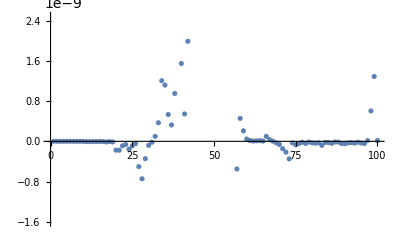

```mathematica
ListPlot[kList]
```

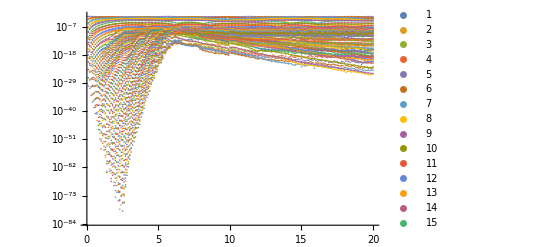

```mathematica
ListLogPlot[solList,PlotLegends->Automatic]
```

Slope

```mathematica
solFun[x_]=fun[dim,x]/.First@sol;
```

```mathematica
solSlopeList=Table[
Table[{x,solFun'[x][[n]]},{x,0,10,0.1}],
{n,1,dim}
];
```

```mathematica
ListLogPlot[solSlopeList]
```

-Graphics-

Time Evolution

```mathematica
evo[t_]:=Module[{solM,solListM,tsampleNM},

solM=NDSolve[eqn,funBare[dim],{x,0,t}];

solListM=Transpose@Table[
Table[{x,fun[dim,x][[n]]/.First@sol},{x,0,t,0.1}],
{n,1,dim}
];





]
```

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

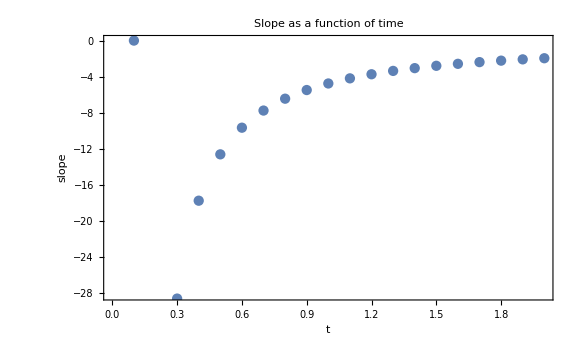

```mathematica
ListPlot[
Table[
{
tindex*0.1,
Coefficient[
Fit[
{#[[1]],Log@#[[2]]}&/@Transpose[solList][[tindex,;;dim/2]],
{1,x},
x
],
x
]
},
{tindex,1,20}
],
Frame->True,ImageSize->Large,PlotLabel->"Slope as a function of time",FrameLabel->{"t","slope"}
]
```

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

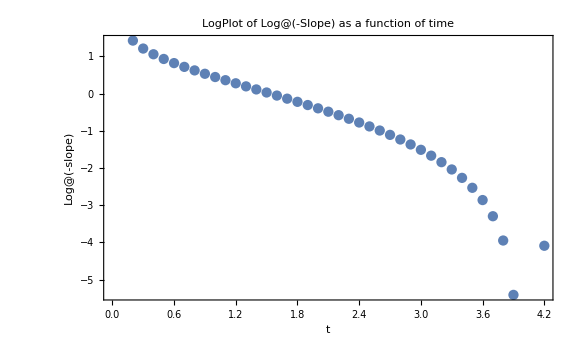

```mathematica
Show[
ListPlot[
Table[
{
tindex*0.1,
Log@Log@-Coefficient[
Fit[
{#[[1]],Log@#[[2]]}&/@Transpose[solList][[tindex,;;dim/2]],
{1,x},
x
],
x
]
},
{tindex,1,200}
],
Frame->True,ImageSize->Large,PlotLabel->"LogPlot of Log@(-Slope) as a function of time",FrameLabel->{"t","Log@(-slope)"}
],
Plot[
CoefficientList[
Fit[
Table[
{
tindex*0.1,
Log@Log@-Coefficient[
Fit[
{#[[1]],Log@#[[2]]}&/@Transpose[solList][[tindex,;;dim/2]],
{1,x},
x
],
x
]
},
{tindex,1,200}
][[20;;60]],
{1,x},
x
],
x
].{1,y},
{y,1,20},PlotStyle->Red
]

]
```

```mathematica
ListAnimate[
Table[ListLogPlot[Transpose[solList][[t,;;,2]],PlotRange->{{0,dim},{10^(-24),1}}],{t,1,20}]
]
```